Interpolation::udeg: Interpolation on unstructured grids is currently only supported for InterpolationOrder->1 or InterpolationOrder->All. Order will be reduced to 1.

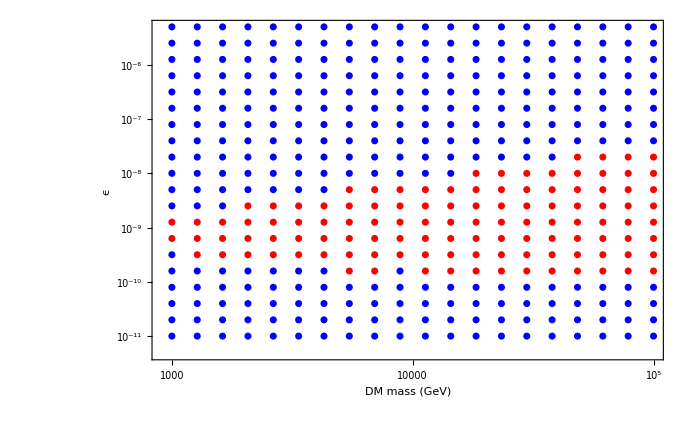

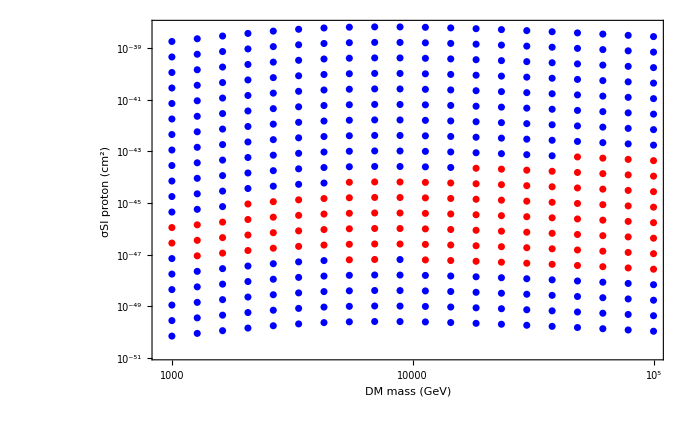

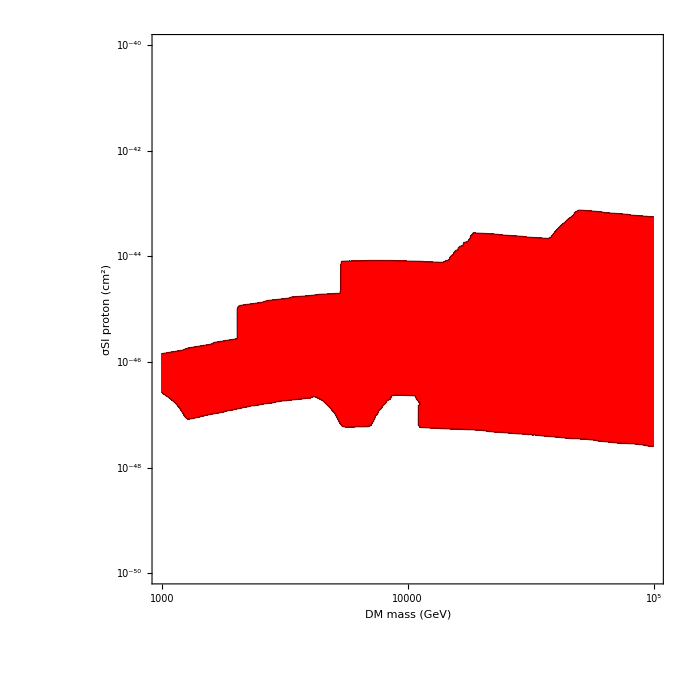

400

```mathematica
SetDirectory[NotebookDirectory[]];
tab=Import["eflux0old","TSV"]//ToExpression;
tab=Flatten[tab,1];
tab;
isexcluded[table_]:=Table[If[table[[i,6,1]]>2.2 10^-12||table[[i,6,2]]>8.8 10^-13||table[[i,6,3]]>2.8 10^-13||table[[i,6,4]]>8.1 10^-14||table[[i,6,5]]>6.3 10^-12,1,0],{i,1,Length[tab]}]
exc=isexcluded[tab];
(*plottab=Table[{exc[[i]],tab[[i,1]],tab[[i,6]]},{i,1,Length[tab]}];*)
exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,4⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,4⟧}]],{i,1,Length[tab]}]
inttab=Table[{{tab⟦i,1⟧,tab⟦i,7⟧},If[exc[[i]]==1,1,0]},{i,1,Length[tab]}];
intfunc=Interpolation[inttab];
ListLogLogPlot[{exctab,allowedtab},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","ϵ"(*σSI proton (cm^2)*)},PlotStyle->{Red,Blue}]
exctab={};
allowedtab={};
Do[If[exc[[i]]==1,exctab=Append[exctab,{tab⟦i,1⟧,tab⟦i,7⟧}]],{i,1,Length[tab]}]
Do[If[exc[[i]]==0,allowedtab=Append[allowedtab,{tab⟦i,1⟧,tab⟦i,7⟧}]],{i,1,Length[tab]}]
ListLogLogPlot[{exctab,allowedtab},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"},PlotStyle->{Red,Blue}]
ContourPlot[intfunc[mχ,σ],{mχ,1000.,100000},{σ,10^-50,10^-40},Contours-> {{0.9}},ContourShading-> {White,Red},ScalingFunctions-> {"Log","Log"},PlotRange-> All,Frame-> True,FrameLabel->{"DM mass (GeV)","σSI proton (cm^2)"}]
Length[tab]
```